This notebook contains a simulation of a controlled inverted pendulum on a cart.

Import dependencies

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

```mathematica
<<draw_inverted_pendulum.m
```

Define constants

```mathematica
(* Acceleration due to gravity in m/s^2 *)
g=9.8;
```

```mathematica
(* The length of the pendulum in m *)
l=0.43;
```

```mathematica
(* The mass of the cart in kg *)
m1=0.103;
```

```mathematica
(* The mass of the pendulum in kg *)
m2=0.066;
```

```mathematica
(* The duration of the simulation in s *)
tMax=5;
```

Define initial conditions

```mathematica
(* The initial angle of the pendulum in rad *)
θ0=Pi/6;
```

```mathematica
(* The initial angular velocity of the pendulum in rad/s *)
ω0=0;
```

```mathematica
(* The initial x position of the cart in m *)
x0=0;
```

```mathematica
(* The initial x velocity of the cart in m/s *)
v0=0;
```

Define the matrices for the continuous simulation

```mathematica
(* The state matrix *)
a={
{0, 1, 0, 0},
{g(m1+m2)/(l m1), 0, 0, 0},
{0,0,0,1},
{g m2/m1,0,0,0}
};
```

```mathematica
(* The input matrix *)
b={
{0},
{1/(l m1)},
{0},
{1/m1}
}
```

{{0},{22.5785},{0},{9.70874}}

```mathematica
(* The state cost matrix *)
q = {
{1,0,0,0},
{0,1,0,0},
{0,0,1,0},
{0,0,0,1}
};
```

```mathematica
(* The input cost matrix *)
r ={{1}};
```

Determine the continuous state feedback matrix via the linear quadratic regulator algorithm

```mathematica
(* The state feedback matrix *)
k=LQRegulatorGains[
StateSpaceModel[{a, b, ConstantArray[0,{4,4}],ConstantArray[0,{4,1}]}],
{q,r}
]
```

{{9.58986,2.1088,-1.,-1.61837}}

Confirm the eigenvalues of the resulting matrix don’t have positive real parts

```mathematica
Eigenvalues[a-b.k]
```

{-25.8756+0. ⅈ,-2.50501+1.46497 ⅈ,-2.50501-1.46497 ⅈ,-1.01544+0. ⅈ}

Generate a plot

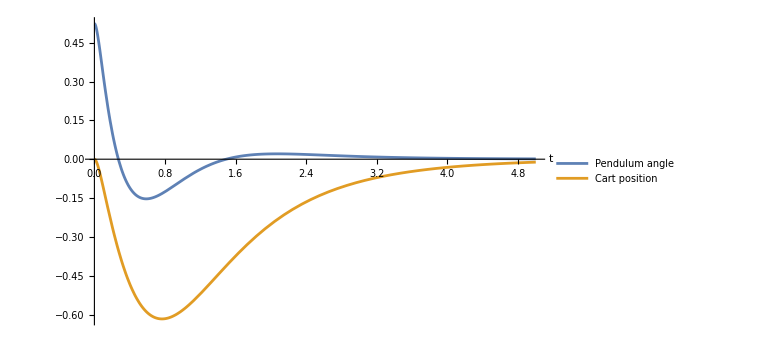

```mathematica
plot=Plot[
{
(MatrixExp[(a-b.k)t].{{θ0},{ω0},{x0},{v0}})[[1,1]],
(MatrixExp[(a-b.k)t].{{θ0},{ω0},{x0},{v0}})[[3,1]]
},
{t,0,tMax},
AxesLabel->{t},
ImageSize->Large,
PlotLegends->{"Pendulum angle","Cart position"}
]
```

Uncomment to export a PNG of the plot

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"controlled.png"}],plot]; *)
```

Generate an animation

```mathematica
Animate[
Module[
{θ,ω,x,v},
{{θ},{ω},{x},{v}}=MatrixExp[(a-b.k)t].{{θ0},{ω0},{x0},{v0}};
drawInvertedPendulum[l,θ,x]
],
{t,0,tMax},
DefaultDuration->tMax
]
```

Uncomment to export a GIF of the animation

```mathematica
(* Export[
FileNameJoin[{NotebookDirectory[],"controlled.gif"}],
Table[
Module[
{θ,ω,x,v},
{{θ},{ω},{x},{v}}=MatrixExp[(a-b.k)t].{{θ0},{ω0},{x0},{v0}};
drawInvertedPendulum[l, θ,x]
],
{t,0,tMax,1/24}
],
DisplayDurations->1/24
];*)
```

Determine the discrete state feedback matrix via the linear quadratic regulator algorithm

```mathematica
(* Sampling period *)
τ=0.002;
```

```mathematica
kd=DiscreteLQRegulatorGains[
StateSpaceModel[{a, b, ConstantArray[0,{4,4}],ConstantArray[0,{4,1}]}],
{q,r},
τ
]
```

{{9.35777,2.05238,-0.968795,-1.56884}}